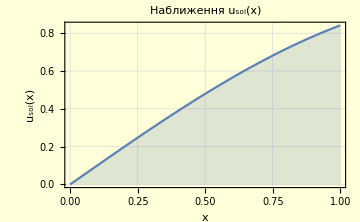
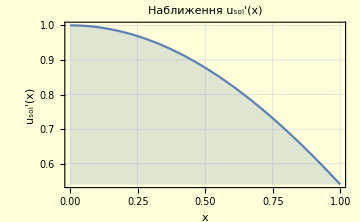

‖u_sol‖_0=0.522184												‖u_sol‖_1=1.

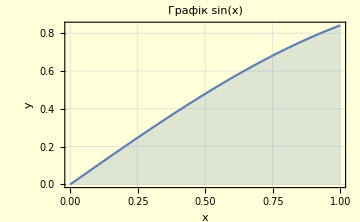

```mathematica
a=0;b=1;f[x_]:=Sin[x];
μ[x_]:=1;β[x_]:=0;σ[x_]:=0;
$MaxPiecewiseCases=700;
Subscript[u, sol]=NDSolveValue[{-(μ'[x]*u'[x]+μ[x] u''[x])+β[x] u'[x]+σ[x] u[x]==f[x],u[a]==0,u'[b]==Cos[1]},u,{x,a,b}];
Subscript[plot1u, sol]=Plot[Subscript[u, sol][x],{x,a,b},FrameLabel->{"x ","u_sol(x) "},PlotLabel->Style[Framed["Наближення u_sol(x)"]],Background->LightYellow,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Subscript[plot2u, sol]=Plot[Subscript[u, sol]'[x],{x,a,b},FrameLabel->{"x ","u_sol'(x) "},PlotLabel->Style[Framed["Наближення u_sol'(x)"]],Background->LightYellow,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Subscript[norma1u, sol]=Sqrt[NIntegrate[Subscript[u, sol][x]^2,{x,a,b}]];
Subscript[norma2u, sol]=Sqrt[NIntegrate[(Subscript[u, sol][x])^2+(Subscript[u, sol]'[x])^2,{x,a,b}]];
Print[Subscript[plot1u, sol],"  ",  Subscript[plot2u, sol]];
Print["‖u_sol‖_0=",Subscript[norma1u, sol],"\t\t\t\t\t\t\t\t\t\t\t\t‖u_sol‖_1=", Subscript[norma2u, sol]];
Print[Plot[y=Sin[x],{x,a,b}, FrameLabel->{"x ","y "},PlotLabel->Style[Framed["Графік sin(x)"]],Background->LightYellow,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium]];
```